```mathematica
gg[h_]:=Plot[x^2+h,{x,-1,1},PlotLegends->Placed[{h},{0.5,h}],PlotRange->{0,4}]
```

```mathematica
Show[Map[gg,{0,1,2,3}]]
```

-Graphics-

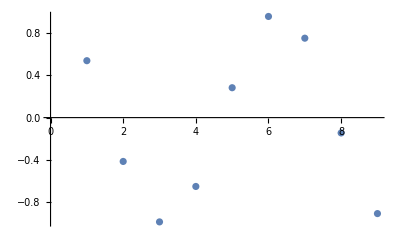

```mathematica
Map[{#,Cos[#]}&,Range[9]]//ListPlot
```

```mathematica
Map[Cos,Range[9]]//N
```

{0.540302,-0.416147,-0.989992,-0.653644,0.283662,0.96017,0.753902,-0.1455,-0.91113}

```mathematica
Range[9]
```

{1,2,3,4,5,6,7,8,9}

```mathematica
x==2
```

x==2

```mathematica
x=2
```

2

```mathematica
x==2
```

True

```mathematica
y===2
```

False

```mathematica
ff[y_]:=If[y===2,"MyTrue","MyFalse"]
```

```mathematica
ff[2]
```

MyTrue

```mathematica
$Failed
```

$Failed

```mathematica
$Failed
```

```mathematica
Clear[x]
```

```mathematica
x^2+y^2==(x+y)^2-2 *x* y
```

x^2+y^2==-2 x y+(x+y)^2

```mathematica
Simplify[x^2+y^2-(-2* x* y+(x+y)^2)]===0
```

True

```mathematica
x^2+y^2===Simplify[(-2* x* y+(x+y)^2)]
```

True

```mathematica
FullForm[Simplify[(-2* x* y+(x+y)^2)]]
```

Plus[Power[x,2],Power[y,2]]

```mathematica
FullForm[(-2* x* y+(x+y)^2)]
```

Plus[Times[-2,x,y],Power[Plus[x,y],2]]

```mathematica
f1[x_]:=x^100
```

```mathematica
f2[x_]=D[f1[x],{x,99}]
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000 x

```mathematica
3^2+4^2===5^2
```

True

```mathematica
f2[y]
```

93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000 y

```mathematica
Reduce[x^2+y>=3&&x>=0&&y>=0]
```

(0≤x≤√3&&y≥3-x^2)||(x>√3&&y≥0)

```mathematica
Resolve
```

```mathematica
$Context
```

```mathematica
Names["Global`*"]
```

{a,A,AllTransitions,AllTransitions$,alpha,AM,AM$,andxp,approx,approxJs,approxJs$,approxSol,approx$,assoc,AssoCritical,AssoCritical$,AssoCritical$15080,AssoNonCritical,AssoNonCritical$,AtHead,AtTail,AuxiliaryGraph,AuxiliaryGraph$,b,BalanceGatheringCurrents,BalanceGatheringCurrents$,BalanceSplittingCurrents,BalanceSplittingCurrents$,BEL,BEL$,BG,BG$,BM,BM$,bool,bool$,bounds,bounds$,c,Compu,consistentCosts,consistentCosts$,ConsistentSwithingCosts,cost,Cost,CostArgs,CostArgs$,costpluscurrents,costpluscurrents$,cost$,cpc1,cpc2,cpc3,crit,CriticalCongestionReduce,CriticalCongestionSolver,CurrentCompCon,CurrentGathering,currents,CurrentSplitting,currents$,d,d2e,Data,Data2Equations,dddRicardo,destination,destination$,e,edge,edge1,edge2,edge$,EE,EEs,EE$,EL,EL$,en1,EntranceVertices,EntranceVertices$,EntryArgs,EntryArgs$,EntryDataAssociation,EntryDataAssociation$,eq,EqBalanceGatheringCurrents,EqBalanceGatheringCurrents$,EqBalanceSplittingCurrents,EqBalanceSplittingCurrents$,EqBalanceSplittingCurrents$11903,EqBalanceSplittingCurrents$15081,EqCompCon,EqCompCon$,EqCompCon$11903,EqCompCon$15081,EqCurrentCompCon,EqCurrentCompCon$,EqCurrentCompCon$11903,EqCurrentCompCon$15081,EqEntryIn,EqEntryIn$,EqEntryIn$11903,EqEntryIn$15081,EqGeneral,EqGeneral$,EqGeneral$15081,EqPosJs,EqPosJs$,EqPosJs$11903,EqPosJs$15081,EqPosJts,EqPosJts$,EqPosJts$11903,EqPosJts$15081,Eqs,EqSwitchingByVertex,EqSwitchingByVertex$,EqSwitchingByVertex$11903,EqSwitchingByVertex$15081,EqTransitionCompCon,EqTransitionCompCon$,EqTransitionCompCon$11903,EqTransitionCompCon$15081,EqValueAuxiliaryEdges,EqValueAuxiliaryEdges$,EqValueAuxiliaryEdges$11903,EqValueAuxiliaryEdges$15081,EVC,EVC$,EVTC,EVTC$,ex3,ex4,ExitCosts,ExitCosts$,ExitCurrents,ExitRules,ExitVertices,ExitVertices$,f,f1,f2,ff,FG,FG$,FinalClean,FinalReduce,FinalReduceStep,FinalStep,fsol,fsol$,fst,fst$,FVL,FVL$,g,G,GetKirchhoffMatrix,gg,groups,groups$,h,H,h$,I1,I121,IncomingEdges,InEdges,InEdges$,InitRules,InitRules$,InitRules$15081,InRules,InRules$,IntM,InwardVertices,InwardVertices$,IsNonLinearSolution,IsSwitchingCostConsistent,j,j1,j10,j11,j12,j2,j3,j4,j5,j6,j7,j8,j9,jargs,jargs$,jjtsR,jjtsR$,js,js$,js$15080,jt1,jt10,jt11,jt12,jt2,jt3,jt4,jt5,jt6,jt7,jt8,jt9,jts,jts$,jtvars,jtvars$,jvars,jvars$,k,Kirchhoff,Kirchhoff$,KM,KM$,LargeCases,LargeCases$,LargeSwitchingTransitions,LargeSwitchingTransitions$,leq,m,M,MaxIter,MaxIter$,MFGPreprocessing,MFGSystemReduce,MFGSystemSolver,ModulesVars,ModulesVars$,ModulesVars$15081,ModuleVars,ModuleVarsNames,ModuleVarsNames$,ModuleVarsNames$15081,ModuleVars$,m$,Ncpc,Ncpc$,newrst,newrst$,newrules,newrules$,NewSystem,NewSystem$,NewSystem$15081,newxp,newxp$,Nlhs,Nlhs$,Nlhs$11903,NN,NNE,NNE$,NNO,NNO$,NNs,NN$,NoDeadEnds,NoDeadEnds$,NoDeadStarts,NoDeadStarts$,NonCriticalList,NonCriticalList$,NonLinear,NonLinearStep,Nrhs,Nrhs$,Nrhs$11903,NumberVectorQ,OO,OR,ORE,ORE$,origin,origin$,ORN,ORN$,ORs,orxp,OR$,OtherWay,OutEdges,OutEdges$,OutgoingEdges,OutRules,OutRules$,OutwardVertices,OutwardVertices$,p,path2triple,pickOne,pickOne$,PreEqs,PreEqs$,PreEqs$15080,p$,RemoveDuplicates,ReplaceSolution,ReZAnd,RoundValues,rst,rst$,RuleBalanceGatheringCurrents,RuleBalanceGatheringCurrents$,RuleBalanceGatheringCurrents$15081,RuleEntryOut,RuleEntryOut$,RuleEntryOut$15081,RuleExitCurrentsIn,RuleExitCurrentsIn$,RuleExitCurrentsIn$15081,RuleExitValues,RuleExitValues$,RuleExitValues$15081,rules,Rules,Rules$,Rules$15081,S,sc,SC,SC$,SignedCurrents,SignedCurrents$,sol,sol$,sorted,sorted$,style,styleg,styleg$,styleg$11903,styler,styler$,styler$11903,style$,style$11903,SwitchingCosts,SwitchingCosts$,Sys2Triple,system,System,System$,t,time,time$,TransitionCompCon,TransitionsAt,Transu,triple2path,TripleClean,TripleStep,u,u1,U1,u10,u11,u12,u2,U2,u3,u4,u5,u6,u7,u8,u9,uargs,uargs$,us,usR,usR$,us$,uvars,uvars$,v,V,vars,vars$,VL,VL$,w,W,x,xi,xi$,xp,x$,y,y$,z,ZAnd,ZeroRun,ZeroRun$}

```mathematica
Names["MFGraphs`*"]
```

{}

```mathematica
Print["SetAttributes[",#,",{Locked}]"]&/@%186
```

SetAttributes[a,{Locked}]

SetAttributes[A,{Locked}]

SetAttributes[AllTransitions,{Locked}]

SetAttributes[AllTransitions$,{Locked}]

SetAttributes[alpha,{Locked}]

SetAttributes[AM,{Locked}]

SetAttributes[AM$,{Locked}]

SetAttributes[andxp,{Locked}]

SetAttributes[approx,{Locked}]

SetAttributes[approxJs,{Locked}]

SetAttributes[approxJs$,{Locked}]

SetAttributes[approxSol,{Locked}]

SetAttributes[approx$,{Locked}]

SetAttributes[assoc,{Locked}]

SetAttributes[AssoCritical,{Locked}]

SetAttributes[AssoCritical$,{Locked}]

SetAttributes[AssoCritical$15080,{Locked}]

SetAttributes[AssoNonCritical,{Locked}]

SetAttributes[AssoNonCritical$,{Locked}]

SetAttributes[AtHead,{Locked}]

SetAttributes[AtTail,{Locked}]

SetAttributes[AuxiliaryGraph,{Locked}]

SetAttributes[AuxiliaryGraph$,{Locked}]

SetAttributes[b,{Locked}]

SetAttributes[BalanceGatheringCurrents,{Locked}]

SetAttributes[BalanceGatheringCurrents$,{Locked}]

SetAttributes[BalanceSplittingCurrents,{Locked}]

SetAttributes[BalanceSplittingCurrents$,{Locked}]

SetAttributes[BEL,{Locked}]

SetAttributes[BEL$,{Locked}]

SetAttributes[BG,{Locked}]

SetAttributes[BG$,{Locked}]

SetAttributes[BM,{Locked}]

SetAttributes[BM$,{Locked}]

SetAttributes[bool,{Locked}]

SetAttributes[bool$,{Locked}]

SetAttributes[bounds,{Locked}]

SetAttributes[bounds$,{Locked}]

SetAttributes[c,{Locked}]

SetAttributes[Compu,{Locked}]

SetAttributes[consistentCosts,{Locked}]

SetAttributes[consistentCosts$,{Locked}]

SetAttributes[ConsistentSwithingCosts,{Locked}]

SetAttributes[cost,{Locked}]

SetAttributes[Cost,{Locked}]

SetAttributes[CostArgs,{Locked}]

SetAttributes[CostArgs$,{Locked}]

SetAttributes[costpluscurrents,{Locked}]

SetAttributes[costpluscurrents$,{Locked}]

SetAttributes[cost$,{Locked}]

SetAttributes[cpc1,{Locked}]

SetAttributes[cpc2,{Locked}]

SetAttributes[cpc3,{Locked}]

SetAttributes[crit,{Locked}]

SetAttributes[CriticalCongestionReduce,{Locked}]

SetAttributes[CriticalCongestionSolver,{Locked}]

SetAttributes[CurrentCompCon,{Locked}]

SetAttributes[CurrentGathering,{Locked}]

SetAttributes[currents,{Locked}]

SetAttributes[CurrentSplitting,{Locked}]

SetAttributes[currents$,{Locked}]

SetAttributes[d,{Locked}]

SetAttributes[d2e,{Locked}]

SetAttributes[Data,{Locked}]

SetAttributes[Data2Equations,{Locked}]

SetAttributes[dddRicardo,{Locked}]

SetAttributes[destination,{Locked}]

SetAttributes[destination$,{Locked}]

SetAttributes[e,{Locked}]

SetAttributes[edge,{Locked}]

SetAttributes[edge1,{Locked}]

SetAttributes[edge2,{Locked}]

SetAttributes[edge$,{Locked}]

SetAttributes[EE,{Locked}]

SetAttributes[EEs,{Locked}]

SetAttributes[EE$,{Locked}]

SetAttributes[EL,{Locked}]

SetAttributes[EL$,{Locked}]

SetAttributes[en1,{Locked}]

SetAttributes[EntranceVertices,{Locked}]

SetAttributes[EntranceVertices$,{Locked}]

SetAttributes[EntryArgs,{Locked}]

SetAttributes[EntryArgs$,{Locked}]

SetAttributes[EntryDataAssociation,{Locked}]

SetAttributes[EntryDataAssociation$,{Locked}]

SetAttributes[eq,{Locked}]

SetAttributes[EqBalanceGatheringCurrents,{Locked}]

SetAttributes[EqBalanceGatheringCurrents$,{Locked}]

SetAttributes[EqBalanceSplittingCurrents,{Locked}]

SetAttributes[EqBalanceSplittingCurrents$,{Locked}]

SetAttributes[EqBalanceSplittingCurrents$11903,{Locked}]

SetAttributes[EqBalanceSplittingCurrents$15081,{Locked}]

SetAttributes[EqCompCon,{Locked}]

SetAttributes[EqCompCon$,{Locked}]

SetAttributes[EqCompCon$11903,{Locked}]

SetAttributes[EqCompCon$15081,{Locked}]

SetAttributes[EqCurrentCompCon,{Locked}]

SetAttributes[EqCurrentCompCon$,{Locked}]

SetAttributes[EqCurrentCompCon$11903,{Locked}]

SetAttributes[EqCurrentCompCon$15081,{Locked}]

SetAttributes[EqEntryIn,{Locked}]

SetAttributes[EqEntryIn$,{Locked}]

SetAttributes[EqEntryIn$11903,{Locked}]

SetAttributes[EqEntryIn$15081,{Locked}]

SetAttributes[EqGeneral,{Locked}]

SetAttributes[EqGeneral$,{Locked}]

SetAttributes[EqGeneral$15081,{Locked}]

SetAttributes[EqPosJs,{Locked}]

SetAttributes[EqPosJs$,{Locked}]

SetAttributes[EqPosJs$11903,{Locked}]

SetAttributes[EqPosJs$15081,{Locked}]

SetAttributes[EqPosJts,{Locked}]

SetAttributes[EqPosJts$,{Locked}]

SetAttributes[EqPosJts$11903,{Locked}]

SetAttributes[EqPosJts$15081,{Locked}]

SetAttributes[Eqs,{Locked}]

SetAttributes[EqSwitchingByVertex,{Locked}]

SetAttributes[EqSwitchingByVertex$,{Locked}]

SetAttributes[EqSwitchingByVertex$11903,{Locked}]

SetAttributes[EqSwitchingByVertex$15081,{Locked}]

SetAttributes[EqTransitionCompCon,{Locked}]

SetAttributes[EqTransitionCompCon$,{Locked}]

SetAttributes[EqTransitionCompCon$11903,{Locked}]

SetAttributes[EqTransitionCompCon$15081,{Locked}]

SetAttributes[EqValueAuxiliaryEdges,{Locked}]

SetAttributes[EqValueAuxiliaryEdges$,{Locked}]

SetAttributes[EqValueAuxiliaryEdges$11903,{Locked}]

SetAttributes[EqValueAuxiliaryEdges$15081,{Locked}]

SetAttributes[EVC,{Locked}]

SetAttributes[EVC$,{Locked}]

SetAttributes[EVTC,{Locked}]

SetAttributes[EVTC$,{Locked}]

SetAttributes[ex3,{Locked}]

SetAttributes[ex4,{Locked}]

SetAttributes[ExitCosts,{Locked}]

SetAttributes[ExitCosts$,{Locked}]

SetAttributes[ExitCurrents,{Locked}]

SetAttributes[ExitRules,{Locked}]

SetAttributes[ExitVertices,{Locked}]

SetAttributes[ExitVertices$,{Locked}]

SetAttributes[f,{Locked}]

SetAttributes[f1,{Locked}]

SetAttributes[f2,{Locked}]

SetAttributes[ff,{Locked}]

SetAttributes[FG,{Locked}]

SetAttributes[FG$,{Locked}]

SetAttributes[FinalClean,{Locked}]

SetAttributes[FinalReduce,{Locked}]

SetAttributes[FinalReduceStep,{Locked}]

SetAttributes[FinalStep,{Locked}]

SetAttributes[fsol,{Locked}]

SetAttributes[fsol$,{Locked}]

SetAttributes[fst,{Locked}]

SetAttributes[fst$,{Locked}]

SetAttributes[FVL,{Locked}]

SetAttributes[FVL$,{Locked}]

SetAttributes[g,{Locked}]

SetAttributes[G,{Locked}]

SetAttributes[GetKirchhoffMatrix,{Locked}]

SetAttributes[gg,{Locked}]

SetAttributes[groups,{Locked}]

SetAttributes[groups$,{Locked}]

SetAttributes[h,{Locked}]

SetAttributes[H,{Locked}]

SetAttributes[h$,{Locked}]

SetAttributes[I1,{Locked}]

SetAttributes[I121,{Locked}]

SetAttributes[IncomingEdges,{Locked}]

SetAttributes[InEdges,{Locked}]

SetAttributes[InEdges$,{Locked}]

SetAttributes[InitRules,{Locked}]

SetAttributes[InitRules$,{Locked}]

SetAttributes[InitRules$15081,{Locked}]

SetAttributes[InRules,{Locked}]

SetAttributes[InRules$,{Locked}]

SetAttributes[IntM,{Locked}]

SetAttributes[InwardVertices,{Locked}]

SetAttributes[InwardVertices$,{Locked}]

SetAttributes[IsNonLinearSolution,{Locked}]

SetAttributes[IsSwitchingCostConsistent,{Locked}]

SetAttributes[j,{Locked}]

SetAttributes[j1,{Locked}]

SetAttributes[j10,{Locked}]

SetAttributes[j11,{Locked}]

SetAttributes[j12,{Locked}]

SetAttributes[j2,{Locked}]

SetAttributes[j3,{Locked}]

SetAttributes[j4,{Locked}]

SetAttributes[j5,{Locked}]

SetAttributes[j6,{Locked}]

SetAttributes[j7,{Locked}]

SetAttributes[j8,{Locked}]

SetAttributes[j9,{Locked}]

SetAttributes[jargs,{Locked}]

SetAttributes[jargs$,{Locked}]

SetAttributes[jjtsR,{Locked}]

SetAttributes[jjtsR$,{Locked}]

SetAttributes[js,{Locked}]

SetAttributes[js$,{Locked}]

SetAttributes[js$15080,{Locked}]

SetAttributes[jt1,{Locked}]

SetAttributes[jt10,{Locked}]

SetAttributes[jt11,{Locked}]

SetAttributes[jt12,{Locked}]

SetAttributes[jt2,{Locked}]

SetAttributes[jt3,{Locked}]

SetAttributes[jt4,{Locked}]

SetAttributes[jt5,{Locked}]

SetAttributes[jt6,{Locked}]

SetAttributes[jt7,{Locked}]

SetAttributes[jt8,{Locked}]

SetAttributes[jt9,{Locked}]

SetAttributes[jts,{Locked}]

SetAttributes[jts$,{Locked}]

SetAttributes[jtvars,{Locked}]

SetAttributes[jtvars$,{Locked}]

SetAttributes[jvars,{Locked}]

SetAttributes[jvars$,{Locked}]

SetAttributes[k,{Locked}]

SetAttributes[Kirchhoff,{Locked}]

SetAttributes[Kirchhoff$,{Locked}]

SetAttributes[KM,{Locked}]

SetAttributes[KM$,{Locked}]

SetAttributes[LargeCases,{Locked}]

SetAttributes[LargeCases$,{Locked}]

SetAttributes[LargeSwitchingTransitions,{Locked}]

SetAttributes[LargeSwitchingTransitions$,{Locked}]

SetAttributes[leq,{Locked}]

SetAttributes[m,{Locked}]

SetAttributes[M,{Locked}]

SetAttributes[MaxIter,{Locked}]

SetAttributes[MaxIter$,{Locked}]

SetAttributes[MFGPreprocessing,{Locked}]

SetAttributes[MFGSystemReduce,{Locked}]

SetAttributes[MFGSystemSolver,{Locked}]

SetAttributes[ModulesVars,{Locked}]

SetAttributes[ModulesVars$,{Locked}]

SetAttributes[ModulesVars$15081,{Locked}]

SetAttributes[ModuleVars,{Locked}]

SetAttributes[ModuleVarsNames,{Locked}]

SetAttributes[ModuleVarsNames$,{Locked}]

SetAttributes[ModuleVarsNames$15081,{Locked}]

SetAttributes[ModuleVars$,{Locked}]

SetAttributes[m$,{Locked}]

SetAttributes[Ncpc,{Locked}]

SetAttributes[Ncpc$,{Locked}]

SetAttributes[newrst,{Locked}]

SetAttributes[newrst$,{Locked}]

SetAttributes[newrules,{Locked}]

SetAttributes[newrules$,{Locked}]

SetAttributes[NewSystem,{Locked}]

SetAttributes[NewSystem$,{Locked}]

SetAttributes[NewSystem$15081,{Locked}]

SetAttributes[newxp,{Locked}]

SetAttributes[newxp$,{Locked}]

SetAttributes[Nlhs,{Locked}]

SetAttributes[Nlhs$,{Locked}]

SetAttributes[Nlhs$11903,{Locked}]

SetAttributes[NN,{Locked}]

SetAttributes[NNE,{Locked}]

SetAttributes[NNE$,{Locked}]

SetAttributes[NNO,{Locked}]

SetAttributes[NNO$,{Locked}]

SetAttributes[NNs,{Locked}]

SetAttributes[NN$,{Locked}]

SetAttributes[NoDeadEnds,{Locked}]

SetAttributes[NoDeadEnds$,{Locked}]

SetAttributes[NoDeadStarts,{Locked}]

SetAttributes[NoDeadStarts$,{Locked}]

SetAttributes[NonCriticalList,{Locked}]

SetAttributes[NonCriticalList$,{Locked}]

SetAttributes[NonLinear,{Locked}]

SetAttributes[NonLinearStep,{Locked}]

SetAttributes[Nrhs,{Locked}]

SetAttributes[Nrhs$,{Locked}]

SetAttributes[Nrhs$11903,{Locked}]

SetAttributes[NumberVectorQ,{Locked}]

SetAttributes[OO,{Locked}]

SetAttributes[OR,{Locked}]

SetAttributes[ORE,{Locked}]

SetAttributes[ORE$,{Locked}]

SetAttributes[origin,{Locked}]

SetAttributes[origin$,{Locked}]

SetAttributes[ORN,{Locked}]

SetAttributes[ORN$,{Locked}]

SetAttributes[ORs,{Locked}]

SetAttributes[orxp,{Locked}]

SetAttributes[OR$,{Locked}]

SetAttributes[OtherWay,{Locked}]

SetAttributes[OutEdges,{Locked}]

SetAttributes[OutEdges$,{Locked}]

SetAttributes[OutgoingEdges,{Locked}]

SetAttributes[OutRules,{Locked}]

SetAttributes[OutRules$,{Locked}]

SetAttributes[OutwardVertices,{Locked}]

SetAttributes[OutwardVertices$,{Locked}]

SetAttributes[p,{Locked}]

SetAttributes[path2triple,{Locked}]

SetAttributes[pickOne,{Locked}]

SetAttributes[pickOne$,{Locked}]

SetAttributes[PreEqs,{Locked}]

SetAttributes[PreEqs$,{Locked}]

SetAttributes[PreEqs$15080,{Locked}]

SetAttributes[p$,{Locked}]

SetAttributes[RemoveDuplicates,{Locked}]

SetAttributes[ReplaceSolution,{Locked}]

SetAttributes[ReZAnd,{Locked}]

SetAttributes[RoundValues,{Locked}]

SetAttributes[rst,{Locked}]

SetAttributes[rst$,{Locked}]

SetAttributes[RuleBalanceGatheringCurrents,{Locked}]

SetAttributes[RuleBalanceGatheringCurrents$,{Locked}]

SetAttributes[RuleBalanceGatheringCurrents$15081,{Locked}]

SetAttributes[RuleEntryOut,{Locked}]

SetAttributes[RuleEntryOut$,{Locked}]

SetAttributes[RuleEntryOut$15081,{Locked}]

SetAttributes[RuleExitCurrentsIn,{Locked}]

SetAttributes[RuleExitCurrentsIn$,{Locked}]

SetAttributes[RuleExitCurrentsIn$15081,{Locked}]

SetAttributes[RuleExitValues,{Locked}]

SetAttributes[RuleExitValues$,{Locked}]

SetAttributes[RuleExitValues$15081,{Locked}]

SetAttributes[rules,{Locked}]

SetAttributes[Rules,{Locked}]

SetAttributes[Rules$,{Locked}]

SetAttributes[Rules$15081,{Locked}]

SetAttributes[S,{Locked}]

SetAttributes[sc,{Locked}]

SetAttributes[SC,{Locked}]

SetAttributes[SC$,{Locked}]

SetAttributes[SignedCurrents,{Locked}]

SetAttributes[SignedCurrents$,{Locked}]

SetAttributes[sol,{Locked}]

SetAttributes[sol$,{Locked}]

SetAttributes[sorted,{Locked}]

SetAttributes[sorted$,{Locked}]

SetAttributes[style,{Locked}]

SetAttributes[styleg,{Locked}]

SetAttributes[styleg$,{Locked}]

SetAttributes[styleg$11903,{Locked}]

SetAttributes[styler,{Locked}]

SetAttributes[styler$,{Locked}]

SetAttributes[styler$11903,{Locked}]

SetAttributes[style$,{Locked}]

SetAttributes[style$11903,{Locked}]

SetAttributes[SwitchingCosts,{Locked}]

SetAttributes[SwitchingCosts$,{Locked}]

SetAttributes[Sys2Triple,{Locked}]

SetAttributes[system,{Locked}]

SetAttributes[System,{Locked}]

SetAttributes[System$,{Locked}]

SetAttributes[t,{Locked}]

SetAttributes[time,{Locked}]

SetAttributes[time$,{Locked}]

SetAttributes[TransitionCompCon,{Locked}]

SetAttributes[TransitionsAt,{Locked}]

SetAttributes[Transu,{Locked}]

SetAttributes[triple2path,{Locked}]

SetAttributes[TripleClean,{Locked}]

SetAttributes[TripleStep,{Locked}]

SetAttributes[u,{Locked}]

SetAttributes[u1,{Locked}]

SetAttributes[U1,{Locked}]

SetAttributes[u10,{Locked}]

SetAttributes[u11,{Locked}]

SetAttributes[u12,{Locked}]

SetAttributes[u2,{Locked}]

SetAttributes[U2,{Locked}]

SetAttributes[u3,{Locked}]

SetAttributes[u4,{Locked}]

SetAttributes[u5,{Locked}]

SetAttributes[u6,{Locked}]

SetAttributes[u7,{Locked}]

SetAttributes[u8,{Locked}]

SetAttributes[u9,{Locked}]

SetAttributes[uargs,{Locked}]

SetAttributes[uargs$,{Locked}]

SetAttributes[us,{Locked}]

SetAttributes[usR,{Locked}]

SetAttributes[usR$,{Locked}]

SetAttributes[us$,{Locked}]

SetAttributes[uvars,{Locked}]

SetAttributes[uvars$,{Locked}]

SetAttributes[v,{Locked}]

SetAttributes[V,{Locked}]

SetAttributes[vars,{Locked}]

SetAttributes[vars$,{Locked}]

SetAttributes[VL,{Locked}]

SetAttributes[VL$,{Locked}]

SetAttributes[w,{Locked}]

SetAttributes[W,{Locked}]

SetAttributes[x,{Locked}]

SetAttributes[xi,{Locked}]

SetAttributes[xi$,{Locked}]

SetAttributes[xp,{Locked}]

SetAttributes[x$,{Locked}]

SetAttributes[y,{Locked}]

SetAttributes[y$,{Locked}]

SetAttributes[z,{Locked}]

SetAttributes[ZAnd,{Locked}]

SetAttributes[ZeroRun,{Locked}]

SetAttributes[ZeroRun$,{Locked}]

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Get
```